# Programa #2

Creación de una función y otros detalles

Transpuesta de m1 = (-3 | -11 | 3
5 | 2 | 1
0 | 1/4 | 2)

Determinante de m1 = 205/2

Vectores propio de m1 = (0.0609139+1.97535 ⅈ | -2.72802+1.05483 ⅈ | 1.
0.0609139-1.97535 ⅈ | -2.72802-1.05483 ⅈ | 1.
0.0225384 | 0.0229466 | 1.)

Dimensión de vectores de m1 = {3,3}

Valores propios de m1 = {-0.545281+6.98087 ⅈ,-0.545281-6.98087 ⅈ,2.09056}

Extracción del elemento 2,3 de m2 = 1/2 (5-√2)

{-3,5,0}

{√3,-ⅈ,1/2 (5-√2)}

{{π,√3,0},{0,-ⅈ,-1},{ϕ,1/2 (5-√2),5}}

{0,-ⅈ,-1}

{0,-ⅈ,-1}

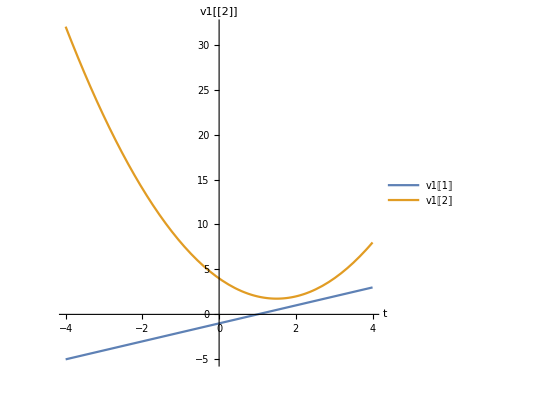

Concatenación de v1 con v2 = {-1+t,4-3 t+t^2,-ⅇ^(-2 t),3,5,7}

Dimensiones de la concatenación de v1 con v2 ={6}

(-1+t | 4-3 t+t^2 | -ⅇ^(-2 t)
3 | 5 | 7)

{2,3}

{{x},{y},{z}}

(Cos[θ1] | -Sin[θ1] | 0 | x
Sin[θ1] | Cos[θ1] | 0 | y
0 | 0 | 1 | z)

(Cos[θ1] | -Sin[θ1] | 0 | x
Sin[θ1] | Cos[θ1] | 0 | y
0 | 0 | 1 | z
0 | 0 | 0 | 1)

```mathematica
(* Algunas operaciones con matrices *)
m1=({{-3, 5, 0}, {-11, 2, 1/4}, {3, 1, 2}});
m2=({{π, 0, ϕ}, {√3, -ⅈ, (5-√2)/2}, {0, -1, 5}});
Print["Transpuesta de m1 = ",Transpose[m1]//MatrixForm]
Print["Determinante de m1 = ",Det[m1]]
Print["Vectores propio de m1 = ",Eigenvectors[m1]//N//MatrixForm]
Print["Dimensión de vectores de m1 = ",Dimensions[Eigenvectors[m1]]]
Print["Valores propios de m1 = ",Eigenvalues[m1]//N]
(* Extracción de elementos de vectores y matrices *)

Print["Extracción del elemento 2,3 de m2 = ",m2[[2,3]]]
m1[[1]]
m2[[2]]
m3=Transpose[m2]
(* Dos formas de extracción de la segunda columna de m2 *)
m3[[2]]
m2[[All,2]]

v1={t-1,t^2-3t+4,-ⅇ^(-2t)};
v2={3,5,7};
Plot[{v1[[1]],v1[[2]]},{t,-4,4},AxesLabel->{"t","v1[[2]]"},
PlotLegends->"Expressions",AspectRatio->1/1]

Print["Concatenación de v1 con v2 = ",Join[v1,v2]]
Print["Dimensiones de la concatenación de v1 con v2 =", Dimensions[Join[v1,v2]]]
Join[{v1,v2},2]//MatrixForm
Dimensions[%]

R1=({{Cos[θ1], -Sin[θ1], 0}, {Sin[θ1], Cos[θ1], 0}, {0, 0, 1}});
P1={x,y,z};
Z1={0,0,0,1};
P1t=Transpose[{P1}]
Join[R1,P1t,2]//MatrixForm
Join[Join[R1,P1t,2],{Z1}]//MatrixForm



(* Creación de una función que toma como entrada 2 cantidades y devuelve la primera como parte real y la segunda como parte imaginaria de un número complejo *)
```